```mathematica
data = Import[NotebookDirectory[] <> "../data/btc future and reference rate/coingecko_future.csv"];
```

```mathematica
data[[1;;3]]
```

( | Date | bitcoin price | Close | log return bitcoin | log return future
0 | 2021-02-03 | 37266.4 | 37790. | 0.0452987 | 0.0337738
1 | 2021-02-02 | 35615.9 | 36535. | 0.059664 | 0.0641463)

```mathematica
dates=Table[DateObject[data[[k,2]]], {k,2,Length[data]}];
```

```mathematica
Length[dates]
```

678

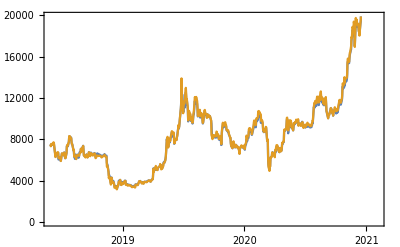

```mathematica
DateListPlot[{{dates,data[[2;;,3]]}ᵀ, {dates, data[[2;;,4]]}ᵀ}]
```

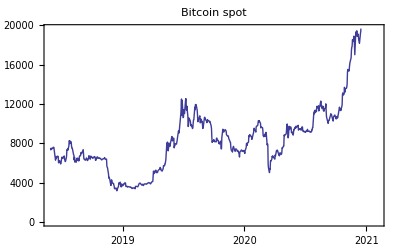

```mathematica
p1=DateListPlot[{dates,data[[2;;,3]]}ᵀ,PlotTheme->"Classic",Joined->True,PlotStyle->Thick,PlotLabel->"Bitcoin spot"]
```

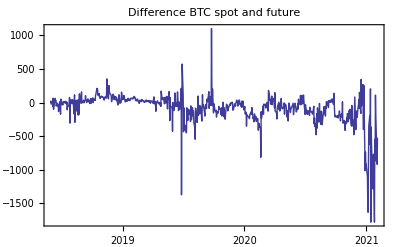

```mathematica
p2=DateListPlot[{dates,data[[2;;,3]]-data[[2;;,4]]}ᵀ,PlotTheme->"Classic",Joined->True,PlotStyle->Thick,PlotLabel->"Difference BTC spot and future",PlotRange->All]
```

```mathematica
r=data⟦2;;All,5⟧;
f=data⟦2;;All,6⟧;
sr=Sort[r];
m=Mean[r];
s=StandardDeviation[r];
l=Length[r];
```

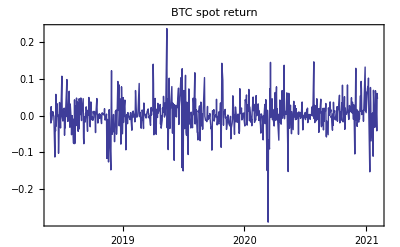

```mathematica
p3=DateListPlot[{dates,r}ᵀ,PlotTheme->"Classic",Joined->True,PlotStyle->Thick,PlotLabel->"BTC spot return",PlotRange->All]
```

```mathematica
extremes=Sort[Abs[r]][[-30;;]];
pos=Flatten[Table[Position[Abs[r],extremes[[k]]], {k,1,Length[extremes]}]];
```

```mathematica
p3a=DateListPlot[{dates[[pos]], r[[pos]]}ᵀ,PlotStyle->{Red,Thick},Joined->False];
```

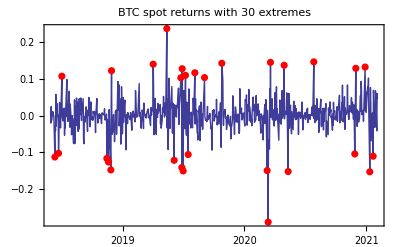

```mathematica
Show[p3,p3a, PlotLabel->"BTC spot returns with 30 extremes"]
```

```mathematica
NMaximize[{LogLikelihood[StudentTDistribution[ν], (r-m)/s],ν>2}, ν]
```

{-930.714,{ν→7.94508}}

Generalized Pareto distribution

```mathematica
K=Ceiling[l 0.05];
u=-sr⟦K⟧
```

0.0652943

```mathematica
y=-sr⟦1;;K-1⟧-u;
```

```mathematica
g[x_,β_,ξ_]:=1-(1+ξ x/β)^(-1/ξ)
```

```mathematica
NMaximize[{Total[Log[g[y,β,ξ]]],ξ>0&& β>0},{β,ξ}]
```

{0.,{β→6.58869×10^-8,ξ→0.203272}}

```mathematica
1/0.203272
```

4.91952

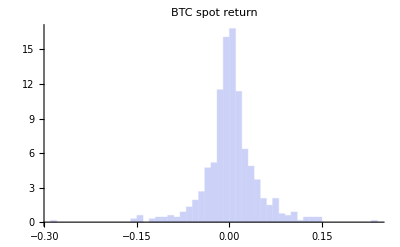

```mathematica
p4=Histogram[data[[2;;,5]],Automatic, "PDF", PlotTheme->"Classic", PlotLabel->"BTC spot return",PlotRange->All]
```

See gretl for summary statistics

```mathematica
t=Table[{InverseCDF[NormalDistribution[m,s],(k-0.5)/l],sr[[k]]}, {k,1,l}];
```

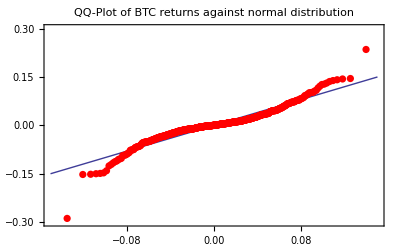

```mathematica
p5=Show[
Plot[x, {x,-0.15, 0.15},PlotTheme->"Classic",PlotRange->{-0.3,0.3}, Frame->True,PlotLabel->"QQ-Plot of BTC returns against normal distribution"],
ListPlot[t, PlotTheme->"Classic", PlotStyle->{Red, PointSize[0.013]},PlotRange->All]
]
```

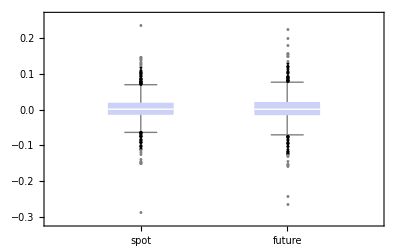

```mathematica
BoxWhiskerChart[{r,f},"Outliers",PlotTheme->"Classic",  ChartLabels->{"spot", "future"}]
```

Outliers are 3/2 times beyond the interquartile range; far outliers are beyond 3 times  the interquartile range.

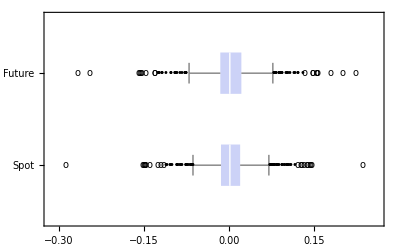

```mathematica
BoxWhiskerChart[{r,f},{{"Outliers", "•"},{"FarOutliers", o}},PlotTheme->"Classic",  ChartLabels->{"Spot", "Future"},BarOrigin->Left]
```

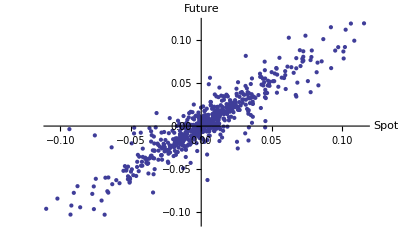

```mathematica
ListPlot[{r,f}ᵀ,PlotTheme->"Classic",AxesLabel->{"Spot", "Future"}]
```